```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*
 This is the code for performing simulation of the general circiut. This circuit can be set as the SR circuit by setting η2=β1=0. Params: @vars - input variables, @tmax - simulation duration, @inst - number of instances generated, @xstartVal - starting value for simulation. Returns: Number of dead individuals, mean lifespan, mortality age for each individual, and full SnC trajectories
*)
simulation[vars_,tmax_,inst_,xstartVal_:-10^10]:=Module[{xstart,proc,dat,out,VV,NOISE,STEP,z,relInd,x,w,t,fast},
STEP = 1;
VV[x_] =Evaluate[((η0+η1 t)(1+η2 x) -  UnitStep[x] (β0(1- β1 t))/(1+x β2)x)/.vars];
NOISE[x_]:=Evaluate[(UnitStep[x] √(2 ϵ))/.vars];
xstart=(If[Length[xstartVal]==0 &&xstartVal==-10^10,0 ,xstartVal]);
proc=ItoProcess[ⅆx[t]==(VV[x]- x UnitStep[-x]) ⅆt +NOISE[x]ⅆw[t] ,x[t],{x,xstart},t,w\[Distributed]WienerProcess[]];
z = RandomFunction[proc,{0.,tmax,1},inst] ;
out = FirstPosition[#,_?(#>(Xcrit/.vars)&)][[1]] & /@ z[[2,1]];
dat=z[[2,1,;;]];
dat=dat/.n_?NumericQ/;n<0->0;
relInd=Complement[Range[1,Dimensions[dat][[1]]],Flatten[Position[out,"NotFound"]]];
(dat[[#,out[[#]];;]]=NA) &/@ relInd;

{Count[out, "NotFound"],N[STEP Mean[DeleteCases[out,"NotFound"]]],out,dat}];
```

```mathematica
(*
These are functions useful for calculating statistics with missing values
*)
CorWithNA[va_,vb_]:=Module[{ind},
ind=Intersection[Flatten[Position[va,_?(NumberQ[#]&)]],Flatten[Position[vb,_?(NumberQ[#]&)]]];
Correlation[va[[ind]],vb[[ind]] ]];
MedianWithNA[v_]:=Module[{},
Median[v[[Flatten[Position[v,_?(NumberQ[#]&)]]]]]];
MeanWithNA[v_]:=Module[{},
Mean[v[[Flatten[Position[v,_?(NumberQ[#]&)]]]]]];
SDWithNA[v_]:=Module[{},
StandardDeviation[v[[Flatten[Position[v,_?(NumberQ[#]&)]]]]]];
SkewnessWithNA[v_]:=Module[{},
Skewness[v[[Flatten[Position[v,_?(NumberQ[#]&)]]]]]];
```

```mathematica
(*
calculates the distribution of slopes in the mice dataset
*)
slopeDistribution[mice_,NORM_]:=Module[{m,tf,allm,slopes},
slopes=LinearModelFit[{#[[1]],#[[2]] NORM}&/@Select[mice[[;;,#,;;]],NumberQ[#[[2]]]&]  ,t,t][[1,2,2]]&/@ Range[Length[mice[[1]]]]];
(*
calculates the distribution of ranks in the mice dataset
*)
rankDistribution[mice_,NORM_]:=Module[{m,tf,allm},
m  =Ordering[mice[[#,;;,2]]] &/@ Range[Length[mice]];
tf = NumberQ[#] &/@mice[[#,;;,2]]&/@ Range[Length[mice]];
allm=MeanWithNA[If[#[[2]],#[[1]]]&/@({m,tf}[[;;,;;,#]]ᵀ)] &/@Range[Length[mice[[1]]]]];
```

```mathematica
(*
calculates the bootstrapped summary statistics of the mice dataset (Mean, Standard Deviation, Skewness, Autocorrelation)
Parameters: @mice is the mice dataset,@NORM is a normalization value for the mice, @iterations is the number of iterations used for bootstrapping
*)
getSummaryStats[mice_,NORM_,iterations_]:=Module[{bootvec,tmpVec,z,va,vb,plots,metric,pts,micemat,samp,t},
bootvec=(tmpVec=Select[##[[2]]& /@#,NumericQ];{#[[1]][[1]],RandomChoice[NORM tmpVec,{iterations,Length[tmpVec]}]})& /@mice;
plots=Table[(
metric={#[[1]],Map[f,#[[2]]]} &/@ bootvec;
pts = {{#[[1]],Mean[#[[2]]]},ErrorBar[StandardDeviation[#[[2]]]]} &/@ metric;
ErrorListPlot[{pts},PlotRange-> All,AxesLabel-> {"Age (days)",SymbolName[f]}]),{f,{Mean,StandardDeviation,Skewness}}];
micemat=##[[2]]& /@#& /@mice;

pts=(va=micemat[[#,;;]];vb=micemat[[#+1,;;]];
z=Map[Function[ii,(samp=RandomChoice[micemat[[{#,#+1},;;]]ᵀ,Dimensions[micemat][[2]]]ᵀ;
CorWithNA[samp[[1]],samp[[2]]])], Range[iterations]];
{{mice[[#,1,1]],Mean[z]},ErrorBar[StandardDeviation[z]]}) &/@Range[1,Dimensions[micemat][[1]]-1];
Flatten[{plots,ErrorListPlot[{pts},PlotRange-> All,AxesLabel-> {"Age (days)","Correlation"}]}]];
```

```mathematica
(*
 estimateLikelihoodTrajectory estimate the likelihood of a single trajectory - that of mouse #ii, from time point #jj to #jj+1.
Parameters: @mice is the mice dataset, @vars are the parameters used, @NORM is a normalization value for the mice dataset, @MONTECARLON is the number of simulations used to estimate the distribution for the log-likelihood
*)
estimateLikelihoodTrajectory[ii_,jj_,mice_,vars_,NORM_,MONTECARLON_]:=Module[{age,x0,x1,score,dist,varsTemp},
(varsTemp = vars;
If[jj==0,age=0,age = mice[[jj,1,1]];];
If[jj==0,x0=0,x0= NORM mice[[jj,ii,2]]];
x1= NORM mice[[jj+1,ii,2]];
If[NumberQ[x0] && NumberQ[x1],
(
varsTemp[[Position[varsTemp,η0][[1,1]]]]=η0-> ((η0+η1 age)/.varsTemp) ;
varsTemp[[Position[varsTemp,β0][[1,1]]]]=β0-> ((β0-β1 age)/.varsTemp) ;
dist=Select[simulation[varsTemp,8 7,MONTECARLON,x0][[4,;;,-1]],NumberQ];

score=LogLikelihood[TruncatedDistribution[{0,Infinity},SmoothKernelDistribution[dist]],{x1}];
score),0])
];
(*
 estimateLikelihoodDataset estimates the likelihood of an entire dataset by iterating through mice. Parameters: @mice is the mice dataset, @vars are the parameters used, @NORM is a normalization value for the mice dataset, @MONTECARLON is the number of simulations used to estimate the distribution for the log-likelihood
Note that for the mice dataset, @CAP the number of MONTECARLON used (MONTECARLON=4000) may fail to estimate occasionally the log-likelihood of a few outlier trajectories. To yield more stable results it is possible to cap very low log-likelihood values at some low value such as LL=-10 or LL=-15. In the manuscript, NORM is set so the average SnC level before 0.5y/o (weeks 8, 16, 24) will be 1.
*)
estimateLikelihoodDataset[mice_,vars_,NORM_,MONTECARLON_,CAP_:False]:=Module[{},
out=Flatten[
Monitor[
Table[
Table[
estimateLikelihoodTrajectory[ii,jj,mice,vars,NORM,MONTECARLON]
,{ii,Range[Length[mice[[1]]]]}]
,{jj,Range[0,Length[mice]-1]}],{ii,jj}]];
If[NumberQ[CAP],If[NumberQ[#] && #>CAP,#,CAP]&/@ out,out]
]
```

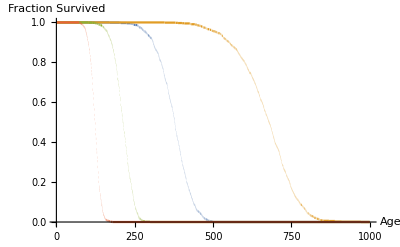
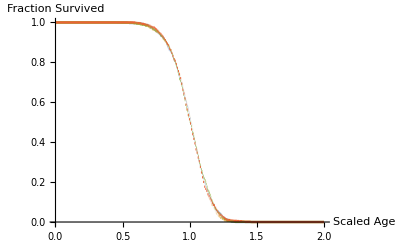
{-Graphics-,-Graphics-,{1.,0.647557,0.432431,0.313562}}

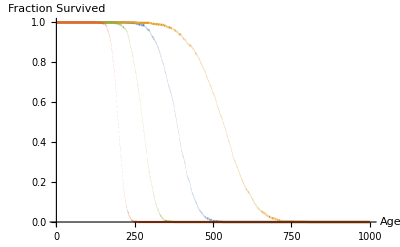
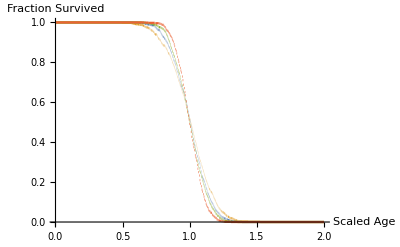
{-Graphics-,-Graphics-,{1.,0.133834,0.340992,0.000290806}}

```mathematica
(*
This function calculates and plots surival curves of the SR model when η1 is scaled by a constant, and tests whether the distributions all collapse when scaled by their mean. Parms: @vars the variables used, @scalingfactors the factors by which η1 will be scaled, @inst the number of instances used, @mxlfspn the maximal lifespan possibly expceted in the simulations.
*)
testScaling[vars_,scalingfactors_,inst_,mxlfspn_]:=Module[{varList,varsTemp,deathdists,scaledDeathdists,surv,survScaled,kspvals},
varList=Table[(varsTemp=vars;varsTemp[[Position[varsTemp,η1][[1,1]]]]=η1->( η1 λ/.vars);
varsTemp),{λ,scalingfactors}];
deathdists = simulation[#,mxlfspn,inst][[3]] &/@ varList;
scaledDeathdists = (#/Mean[#]) &/@ deathdists;
surv=SurvivalModelFit[#][t]  &/@ deathdists;

survScaled=SurvivalModelFit[#][t]  &/@ scaledDeathdists;
kspvals = KolmogorovSmirnovTest[scaledDeathdists[[1]],#] &/@ scaledDeathdists;
{Plot[surv,{t,0,mxlfspn},AxesLabel->{"Age","Fraction Survived"},PlotRange->{0,1}],Plot[survScaled,{t,0,2},AxesLabel->{"Scaled Age","Fraction Survived"},PlotRange->{0,1}],kspvals}
]
testScaling[{η0-> 0,η1-> 0.07/24,η2-> 0,β0-> 1,β1-> 0,β2-> 1,ϵ-> 1,Xcrit-> 20},{1,0.5,2,4},1000,1000]
testScaling[{η0-> 0,η1-> 0.006/24,η2-> 0,β0-> 0,β1-> 0,β2-> 1,ϵ-> 0.037,Xcrit-> 20},{1,0.5,2,4},1000,1000]
```